```mathematica
(*Max quantum state number and system time*)
qubit=5;
t=10;
ExactMaxQ=4;
```

```mathematica
(*Governing matrix list and initial state list *)
GovernMatQuanList=List[];
InitStateQuanList=List[];
(*the exact value accordingly*)
GovernMatQuanListExact=List[];
InitStateQuanListExact=List[];
Do[
If[i≤ExactMaxQ,
QCTMC=QueueInit[2,i,"A"];
GovME=GovernMat[QCTMC];
InitStateE=L2V[QCTMC,RandomInitState[QCTMC,"A"]];
AppendTo[GovernMatQuanListExact,GovME];
AppendTo[InitStateQuanListExact,InitStateE];
GovMN=N[GovME];
InitStateN=N[InitStateE];,
QCTMC=QueueInit[2,i,"N"];
GovMN=GovernMat[QCTMC];
InitStateN=L2V[QCTMC,RandomInitState[QCTMC,"N"]];
];
AppendTo[GovernMatQuanList,GovMN];
AppendTo[InitStateQuanList,InitStateN];
,{i,1,qubit}]
```

```mathematica
(* Exact Value *)
ExactQuanList=List[];
ExactQuanInitList=List[];
Do[
GovM=GovernMatQuanListExact[[i]];
ExactRes=MatrixExp[GovM*t];
ExactInit=Flatten[ExactRes.InitStateQuanListExact[[i]]];
AppendTo[ExactQuanList,ExactRes];
AppendTo[ExactQuanInitList,ExactInit];
,{i,1,ExactMaxQ}]
```

```mathematica
(*Numerical Method for transient analysis without an initial state*)
ssTimeQuanList=List[];
PadeTimeQuanList=List[];
KryTimeQuanList=List[];
ssErrorQuanList=List[];
PadeErrorQuanList=List[];
KryErrorQuanList=List[];
Do[
ssRes=AbsoluteTiming[ExpSS[GovernMatQuanList[[i]]*t]];
PadeRes=AbsoluteTiming[MatrixExp[GovernMatQuanList[[i]]*t,Method->"Pade"]];
KryRes=AbsoluteTiming[MatrixExp[GovernMatQuanList[[i]]*t,Flatten[N[InitStateQuanList[[i]]]],Method->"Krylov"]];
AppendTo[ssTimeQuanList,ssRes[[1]]];
AppendTo[PadeTimeQuanList,PadeRes[[1]]];
AppendTo[KryTimeQuanList,KryRes[[1]]];
If[i≤4,
AppendTo[ssErrorQuanList,Max[Abs[ssRes[[2]]-ExactQuanList[[i]]]]];
AppendTo[PadeErrorQuanList,Max[Abs[PadeRes[[2]]-ExactQuanList[[i]]]]];
AppendTo[KryErrorQuanList,Max[Abs[KryRes[[2]]-ExactQuanInitList[[i]]]]];
];
,
{i,1,qubit}]
```

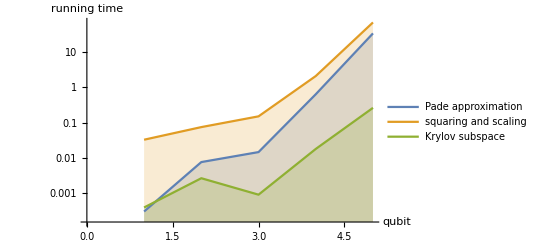

```mathematica
OverallQuantumTime=ListLinePlot[{PadeTimeQuanList,ssTimeQuanList,KryTimeQuanList},Filling->Axis,PlotLegends->{"Pade approximation","squaring and scaling","Krylov subspace"},AxesLabel->{"qubit","running time"},ScalingFunctions->"Log"]
```

```mathematica
Export[NotebookDirectory[]<>"EPS_figure\\OverallQuantumTime.eps",OverallQuantumTime]
```

C:\Users\mei\Desktop\Transient Analysiso of QCTMC\Code\EPS_figure\OverallQuantumTime.eps

```mathematica
PadeTimeQuanList
```

{0.0005155,0.0053565,0.0327992,0.709834,32.7567}

```mathematica
ssTimeQuanList
```

{0.032636,0.0742843,0.149808,2.0752,68.4588}

```mathematica
KryTimeQuanList
```

{0.0005947,0.0039976,0.0013338,0.0188524,0.358837}

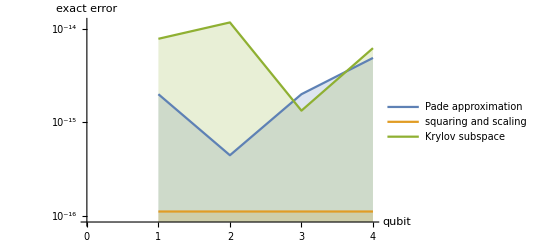

```mathematica
OverallQuantumAcu=ListLinePlot[{PadeErrorQuanList,ssErrorQuanList,KryErrorQuanList},Filling->Axis,PlotLegends->{"Pade approximation","squaring and scaling","Krylov subspace"},AxesLabel->{"qubit","exact error"},ScalingFunctions->"Log"]
```

```mathematica
Export[NotebookDirectory[]<>"EPS_figure\\OverallQuantumAcu.eps",OverallQuantumAcu]
```

C:\Users\mei\Desktop\Transient Analysiso of QCTMC\Code\EPS_figure\OverallQuantumAcu.eps

```mathematica
PadeErrorQuanList
```

{1.9984×10^-15,4.44089×10^-16,1.9984×10^-15,4.88498×10^-15}

```mathematica
ssErrorQuanList
```

{1.11022×10^-16,1.11022×10^-16,1.11022×10^-16,1.11022×10^-16}

```mathematica
KryErrorQuanList
```

{7.82707×10^-15,1.17129×10^-14,1.33227×10^-15,6.21725×10^-15}